# Gaussian Error Propagation for v2dir

```mathematica
ClearAll["Global`*"]
```

```mathematica
v2dir = (Rgam v2inc - v2dec)/(Rgam -1);
```

```mathematica
dRgam = D[v2dir, Rgam]//Simplify
```

(v2dec-v2inc)/(-1+Rgam)^2

```mathematica
dv2inc = D[v2dir, v2inc] // Simplify
```

Rgam/(-1+Rgam)

```mathematica
dv2dec = D[v2dir, v2dec] // Simplify
```

1/(1-Rgam)

```mathematica
SigmaV2dirSquared = dRgam^2 SigmaRgam^2+ dv2inc^2 SigmaV2inc^2+dv2dec^2 SigmaV2dec^2
```

SigmaV2dec^2/(1-Rgam)^2+(Rgam^2 SigmaV2inc^2)/(-1+Rgam)^2+(SigmaRgam^2 (v2dec-v2inc)^2)/(-1+Rgam)^4

```mathematica
SigmaV2dirSquared//FullSimplify//CForm
```

(Power(-1 + Rgam,2)*(Power(SigmaV2dec,2) + Power(Rgam,2)*Power(SigmaV2inc,2)) + Power(SigmaRgam,2)*Power(v2dec - v2inc,2))/Power(-1 + Rgam,4)

## Significance for the hypothesis v2dir = 0

```mathematica
sig= v2dir / √SigmaV2dirSquared
```

(-v2dec+Rgam v2inc)/((-1+Rgam) √(SigmaV2dec^2/(1-Rgam)^2+(Rgam^2 SigmaV2inc^2)/(-1+Rgam)^2+(SigmaRgam^2 (v2dec-v2inc)^2)/(-1+Rgam)^4))

```mathematica
sig2= sig//FullSimplify
```

(-v2dec+Rgam v2inc)/((-1+Rgam) √(((-1+Rgam)^2 (SigmaV2dec^2+Rgam^2 SigmaV2inc^2)+SigmaRgam^2 (v2dec-v2inc)^2)/(-1+Rgam)^4))

```mathematica
ntmp=(Numerator[sig] / Rgam) // Simplify
```

-v2dec/Rgam+v2inc

```mathematica
dtmp= Sqrt[Denominator[sig*sig]/(Rgam Rgam)] //FullSimplify
```

√((SigmaV2dec^2+Rgam^2 SigmaV2inc^2+(SigmaRgam^2 (v2dec-v2inc)^2)/(-1+Rgam)^2)/Rgam^2)

```mathematica
sig3=ntmp/dtmp
```

(-v2dec/Rgam+v2inc)/(√((SigmaV2dec^2+Rgam^2 SigmaV2inc^2+(SigmaRgam^2 (v2dec-v2inc)^2)/(-1+Rgam)^2)/Rgam^2))

```mathematica
pars1={v2inc->0.1814, SigmaV2inc->0.0028, v2dec->0.1824, SigmaV2dec->0.0046, Rgam->1.061, SigmaRgam->0.048};
```

```mathematica
sig3/.pars1
```

1.81943

## Significance from the Bayesian-inspired method

```mathematica
g=PDF[NormalDistribution[v2DecPar/RgamPar,SigmaV2inc],v2IncPar];
```

```mathematica
pi1 = PDF[NormalDistribution[v2dec,SigmaV2dec],v2DecPar];
```

```mathematica
pi2= PDF[NormalDistribution[Rgam,SigmaRgam],RgamPar];
```

```mathematica
f= g pi1 pi2 ;
```

```mathematica
f2=Integrate[f, {v2DecPar,-∞, ∞},Assumptions->{RgamPar>1, SigmaRgam>0, SigmaV2dec>0, SigmaV2inc>0}]//FullSimplify;
```

```mathematica
f2p= f2/.pars1;
```

```mathematica
L[v2IncVal_]:=NIntegrate[f2p /. {v2IncPar->v2IncVal}, {RgamPar, 1., 1.4}]
```

```mathematica
gausErrProp[v2incv_]:=PDF[NormalDistribution[v2dec/Rgam,Denominator[sig3]],v2incv] /. pars1;
```

```mathematica
Normfac = L[v2dec/Rgam /. pars1] / gausErrProp[v2dec/Rgam /. pars1] ;
```

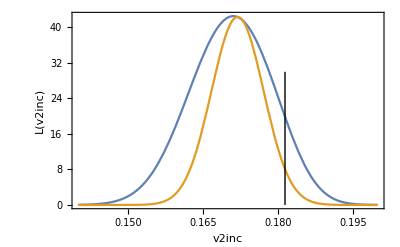

```mathematica
Plot[{L[v2incv],Normfac gausErrProp[v2incv]}, {v2incv, .14, 0.2},Frame->True,FrameLabel->{Style["v2inc",16],Style["L(v2inc)",16]},Epilog->Line[{{v2inc/.pars1,0},{v2inc/.pars1,30}}]]
```

```mathematica
norm=NIntegrate[f2p , {v2IncPar, 0., 0.3}, {RgamPar, 1., 1.3}]
```

0.898106

```mathematica
meanL = NIntegrate[v2IncPar f2p , {v2IncPar, 0., 0.3}, {RgamPar, 1., 1.3}]/norm
```

0.170626

```mathematica
VarL = NIntegrate[(v2IncPar - meanL)^2 f2p , {v2IncPar, 0., 0.3}, {RgamPar, 1., 1.3}]/norm
```

0.0000666808

```mathematica
SigmaL=Sqrt[VarL]
```

0.00816583

```mathematica
sigBayesianInspired=(v2inc-meanL)/SigmaL /.pars1
```

1.31944